```mathematica
Needs["Cosmology`"]
```

```mathematica
Convert[HubbleConstant,1/Second]
```

3.24077928966×10^-18 Second^-1

```mathematica
mp0=Import["~/jennaproject/data/test_matterPower_0.dat","Table"];
transRat=Import["~/jennaproject/data/Gru.txt","Table"];
k=mp0[[All,1]];
```

```mathematica
Dimensions[mp0]
```

{496,2}

```mathematica
Dimensions[transRat]
```

{140,2}

### Interpolation for Power Spectrum

InterpolatingFunction::dmval: Input value {-9.210340371976182`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-9.21013812949874`} lies outside the range of data in the interpolating function. Extrapolation will be used.

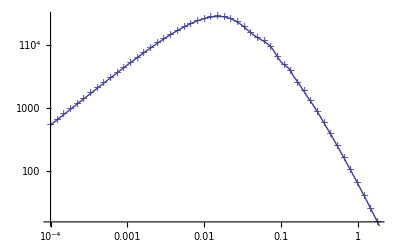

```mathematica
α=ListLogLogPlot[Thread[{Take[k,{1,496,10}],Take[mp0[[All,2]],{1,496,10}]}],PlotMarkers->"+"] ;(* Power Spectrum, to interpolate *)
Pk1=Interpolation[mp0];
β=LogLogPlot[Pk1[p],{p,0.0001,1.993}];
Show[α,β] (* Tests interpoloation of mp0 *)
```

### Interpolation for G_u

```mathematica
TR=Interpolation[transRat];
```

```mathematica
α1=ListLogLogPlot[Thread[{Take[transRat[[All,1]],{1,140,4}],Take[transRat[[All,2]],{1,140,4}]}],PlotMarkers->"+"];
β1=LogLogPlot[TR[n],{n,1.9755223192*10^(-7),12}];
```

InterpolatingFunction::dmval: Input value {-15.437262822152327`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-15.436896697833115`} lies outside the range of data in the interpolating function. Extrapolation will be used.

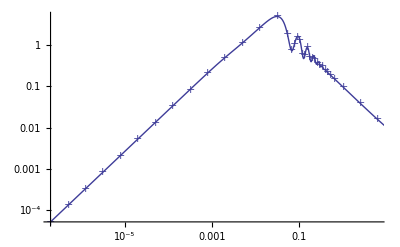

```mathematica
Show[α1,β1] (* Tests interpolation of Gru *)
```

## Equilateral Triangle

### First term, eqn 3.10, Yoo et al.

```mathematica
F2ab=F2bc=F2ac=0.29;
μab=-0.99;
h=0.703;
```

```mathematica
normBg1 = 2*(mp0[[All,2]])^2*(F2ab+F2bc+F2ac);
```

```mathematica
eqterm1=ListLogLogPlot[Thread[{k,normBg1/h^6}],Joined->True,PlotRange->{{.005,.3},{10^4,10^11}},Frame->True,PlotStyle->{Thick,Red}];
```

### Second term

```mathematica
bias2 = 0.1;
normBg2=1/2*bias2*3*(mp0[[All,2]])^2;
```

```mathematica
eqterm2=ListLogLogPlot[Thread[{k,normBg2/h^6}],Joined->True,PlotRange->{{.005,.3},{10^4,10^11}},Frame->True,PlotStyle->{Thick,Orange}];
```

### Third term

```mathematica
bias3 = 0.01;
normBg3=3*bias3*(2*Pk1[p]^2*-TR[p]^2*μab);
```

```mathematica
eqterm3=LogLogPlot[normBg3/h^6,{p,0.001,1.993},PlotRange->{{.005,.3},{10^4,10^11}},Frame->True,PlotStyle->{Thick,Blue}];
```

InterpolatingFunction::dmval: Input value {-6.907600075028738`} lies outside the range of data in the interpolating function. Extrapolation will be used.

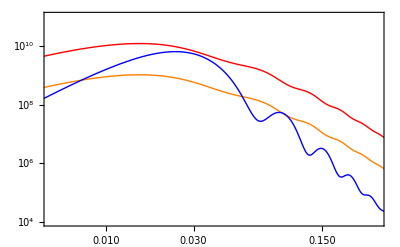

```mathematica
Show[eqterm1,eqterm2,eqterm3]
```

## Isosceles Triangle

### First Term

```mathematica
F2ab=0.004;
F2bc=F2ac=0.46;
μbc=μac=-0.07;
```

```mathematica
isnormBg1 = 2*(Pk1[p]^2*F2ab+Pk1[p]*Pk1[p*Sqrt[2+2*μ]]*(F2bc+F2ac));
isterm1=LogLogPlot[isnormBg1/h^6,{p,0.001,1.993},PlotRange->{{.005,.3},{10^4,10^11}},Frame->True,PlotStyle->{Thick,Red}];
```

InterpolatingFunction::dmval: Input value {-6.907600075028738`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-6.752551170534599`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

### Second Term

```mathematica
isnormBg2=bias2/2*(Pk1[p]^2+2*Pk1[p]*Pk1[p*Sqrt[2+2*μ]]);
```

```mathematica
isterm2=LogLogPlot[isnormBg2/h^6,{p,0.001,1.993},PlotRange->{{.005,.3},{10^4,10^11}},Frame->True,PlotStyle->{Thick,Orange}];
```

InterpolatingFunction::dmval: Input value {-6.907600075028738`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-6.752551170534599`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

### Third Term

```mathematica
isnormBg3=2*bias3*(Pk1[p]^2*-TR[p]^2*μab+2*Pk1[p]*Pk1[p*Sqrt[2+2*μ]]*-TR[p]*TR[p*Sqrt[2+2*μ]]*μbc);
isterm3=LogLogPlot[isnormBg3/h^6,{p,0.001,1.993},PlotRange->{{.005,.3},{10^4,10^11}},Frame->True,PlotStyle->{Thick,Blue}];
```

InterpolatingFunction::dmval: Input value {-6.907600075028738`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

```mathematica
Show[isterm1,isterm2,isterm3]
```

-Graphics-